```mathematica
Zeta[2.0]//Timing
```

{0.000051,1.64493}

```mathematica
1+1/2^2+1/3^2+1/4^2+1/5^2+1/6^2//N
```

1.49139

```mathematica
Table[1/k^2,{k,1,500}]
```

```mathematica
Total[Table[1/k^2,{k,1,119999}]]//N//Timing
```

{0.433825,1.64493}

```mathematica
sum=0;
For[k=1,(*initialization*)
k<=119999,(*condition*)
k++, (*increment*)
sum=sum+1/k^2 (*body*)
]
```

```mathematica
sum//N
```

1.64493

```mathematica
Timing[sum=0;
For[k=1,k<=119999,k++,sum=sum+1/k^2];
sum//N]
```

{1.28298,1.64493}

```mathematica
For[n=1;x[0]=1,
n<=100,n++,
x[n]= -0.5x[n-1]+Log[Abs[x[n-1]]]]
```

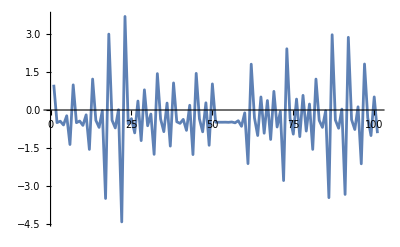

```mathematica
ListPlot[Table[x[n],{n,0,100}],Joined->True]
```

```mathematica
f[t_,x_]=-2x;
xi=1;
ti=0;
tf=10;
nmax=100;
h=(tf-ti)/nmax//N;
datalist={};
xprev=xi;
tprev=ti;
datalist=Append[datalist,{tprev,xprev}];
For[n=1,
      n<=nmax,
      n++,
      tnext=tprev+h;
      xnext=xprev+ h  f[tprev,xprev];
     datalist=Append[datalist,{tnext,xnext}];
     xprev=xnext;
     tprev=tnext;
]
```

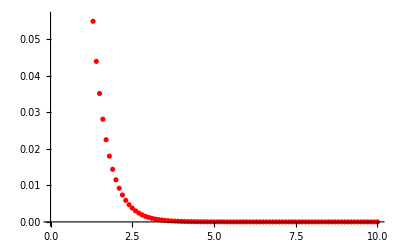

```mathematica
dataplot=ListPlot[datalist,PlotStyle->Red]
```

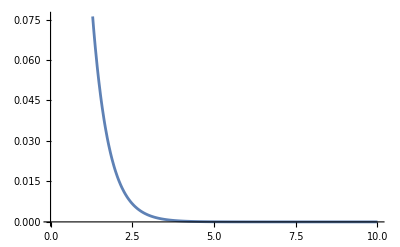

```mathematica
solutionplot=Plot[Exp[-2t],{t,ti,tf}]
```

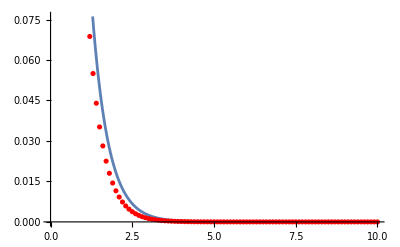

```mathematica
Show[solutionplot,dataplot]
```